0.656297

0.00270367-1.30795×10^-17 ⅈ

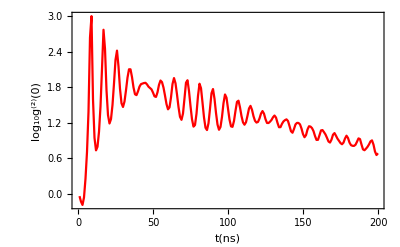

```mathematica
Clear["Global`*"];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=16;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
matrixvariablef=columnlengthf*columnlengthf;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f;
Jrf=σr1f+σr2f+σr3f+σr4f;
Jxf=Jlf+Jrf;






(*设定参数*)
ωr=4*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;

γ=0.1*g;
κ=0.1*g;


Ω1=0;
Ω2=0;
Ω3=0;
Ω4=0;
φ=0;

E1=3*κ;
t0=200;
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columnlengthf},{columnlengthf}];
For[i=0,i<columnlengthf,i++;
For[j=0,j<columnlengthf,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωr*adaigef.af+g*(adaigef.adaigef.(σl1f)+af.af.(σr1f))+g*(adaigef.adaigef.(σl2f)+af.af.(σr2f))+g*(adaigef.adaigef.(σl3f)+af.af.(σr3f))+g*(adaigef.adaigef.(σl4f)+af.af.(σr4f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)

ωd=ωr-28*κ;
H1=H+E1*Cos[ωd*t]*(adaigef+af); 

(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1-H1.ρf)+κ/2*(2*af.ρf.adaigef-ρf.adaigef.af-adaigef.af.ρf)+γ/2*(2*σl1f.ρf.σr1f-ρf.σr1f.σl1f-σr1f.σl1f.ρf)+γ/2*(2*σl2f.ρf.σr2f-ρf.σr2f.σl2f-σr2f.σl2f.ρf)+γ/2*(2*σl3f.ρf.σr3f-ρf.σr3f.σl3f-σr3f.σl3f.ρf)+γ/2*(2*σl4f.ρf.σr4f-ρf.σr4f.σl4f-σr4f.σl4f.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columnlengthf,i++;
For[j=0,j<columnlengthf,j++;
equ[[((i-1)*columnlengthf+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];
(*生成初值*)
ρinitialatom=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]];
For[i=0,i<columnlengthf,i++;
For[j=0,j<columnlengthf,j++;
equ[[matrixvariablef+(((i-1)*columnlengthf+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columnlengthf,i++;
For[j=0,j<columnlengthf,j++;
equvariable[[((i-1)*columnlengthf+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columnlengthf},{columnlengthf}];
For[i=0,i<columnlengthf,i++;
For[j=0,j<columnlengthf,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columnlengthf+j)]]
]
];

G20=Tr[adaigef.adaigef.af.af.ρsolutionf]/((Abs[Tr[adaigef.af.ρsolutionf]])^2);
dataG20=Table[{t,Log10[Abs[G20]]},{t,1,t0}];
t=t0-1;
Log10[Abs[G20]]
averp=Tr[adaigef.af.ρsolutionf]



ListPlot[dataG20,FrameLabel->{"t(ns)","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotStyle->{Red},Frame->True,PlotRange->All]
```

```mathematica
data={{30,0.22831923998261236},{29,0.24886131628052574},{28,0.2873228117419861},{27,0.3086857931417816},{26,0.36603668357695085},{25,0.38344712589370883},{24,0.434330508893768},{23,0.493254260575062},{22,0.5022614720624496},{21,0.6171364056870854},{20,0.7074829966071972},{19,0.8197006214059306},{18,0.9589361744612438},{17,1.3892399403784668},{16,1.4358699224279},{15,1.1831678789666884},{14,0.7934246615816972},{13,0.9947457855403212},{12,0.7951455421035794},{11,0.46300815439106985},{10,-0.04311710258343963},{9,-0.36392174873621763},{8,-0.5451726470381495},{7,-0.8593962093746572},{6,-1.244298850964097},{5,-1.6469983081729653},{4,-1.8956098497788998},{3,-2.411305061498213},{2,-2.868276214590952},{1,-3.3126243624321994},{0,-3.546148430871985},{-30,0.22831923998261236},{-29,0.24886131628052574},{-28,0.2873228117419861},{-27,0.3086857931417816},{-26,0.36603668357695085},{-25,0.38344712589370883},{-24,0.434330508893768},{-23,0.493254260575062},{-22,0.5022614720624496},{-21,0.6171364056870854},{-20,0.7074829966071972},{-19,0.8197006214059306},{-18,0.9589361744612438},{-17,1.3892399403784668},{-16,1.4358699224279},{-15,1.1831678789666884},{-14,0.7934246615816972},{-13,0.9947457855403212},{-12,0.7951455421035794},{-11,0.46300815439106985},{-10,-0.04311710258343963},{-9,-0.36392174873621763},{-8,-0.5451726470381495},{-7,-0.8593962093746572},{-6,-1.244298850964097},{-5,-1.6469983081729653},{-4,-1.8956098497788998},{-3,-2.411305061498213},{-2,-2.868276214590952},{-1,-3.3126243624321994}};ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-5,3}},PlotMarkers->"▽",AspectRatio->1]
```

-Graphics-

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

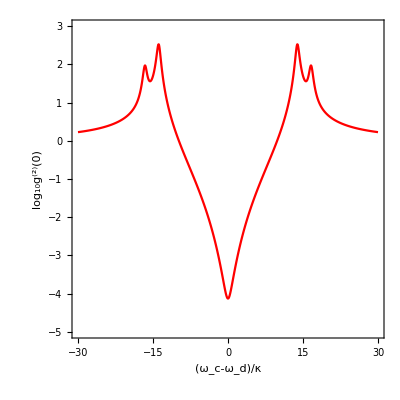

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[100];



data=ParallelTable[
ωr=4*2*Pi;
ωq=8*2*Pi;
Na=4;


γ=0.001*ωr;
κ=0.001*ωr;
E1=3*κ;
max1=30*κ;
min1=-30*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
C1=√(E1^2/(2 E1^2+4 Δ^2+κ^2));

g=0.01*ωr;


equs=Table[{g*C2*√2+E1/2*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C2",ToString[i]]]+2*Δ*ToExpression[StringJoin["C2",ToString[i]]]==0,g*C3*√6+E1/2*ToExpression[StringJoin["C2",ToString[i]]]-I/2*κ*ToExpression[StringJoin["C3",ToString[i]]]-I/2*γ*ToExpression[StringJoin["C3",ToString[i]]]+Δ*ToExpression[StringJoin["C3",ToString[i]]]+2*Δ*ToExpression[StringJoin["C3",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,(Sum[g*√2*ToExpression[StringJoin["C2",ToString[i]]],{i,Na}])+E1/2*C1*√2+E1/2*C3*√3-I*κ*C2+2*Δ*C2==0];
equs=Append[equs,(Sum[g*√6*ToExpression[StringJoin["C3",ToString[i]]],{i,Na}])+E1/2*C2*√3-I/2*κ*C3*3+3*Δ*C3==0];

vars={C2,C3,Table[ToExpression[StringJoin["C2",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["C3",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
C3data=C3/.S[[1,2]];
logg20=Log10[(Abs[C2data]^2*2+Abs[C3data]^2*6)/((E1^2/(2 E1^2+4 Δ^2+κ^2))^2)];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_c-ω_d)/κ","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->True,PlotStyle->{Red},Frame->True,PlotRange->{{-30,30},{-5,3}},AspectRatio->1]
```

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Export["figs3.eps",-Graphics-]
```

figs3.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figs3.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["figs3.eps"]]]
```